## Tsetlin Automatons

A two-state Tsetlin Automaton is represented by a positive integer (representing the current state):

```mathematica
3
```

3

Approach is a helper function that takes three inputs, (x, y, t) and outputs x shiftedt closer to y (unless x==y, in which case x is outputted).

```mathematica
Approach[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=
Which[
x==y,x,
x>y,x-t,
x<y,x+t]
```

```mathematica
Approach[3,6,1]
```

4

Most Tsetlin Automaton-related functions take at least the following two arguments as input: the state as well as the state identifier ( a number n such that the total number of states = 2n).

TsetlinAction is a function that takes a current state as well as a state identifier, and outputs a 1 or a 2 (useful for indexing) depending on how the current state compares to the state identifier.

```mathematica
TsetlinAction[t_Integer,si_Integer]:=
If[
t>si,
2,
1]
```

TsetlinPunish and TsetlinReward both take a state and a state identifier as input and punish/reward the Tsetlin automaton. The output is the new state of the Tsetlin Automaton.

```mathematica
TsetlinPunish[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,1,1],
Approach[t,2*si,1]]
```

```mathematica
TsetlinReward[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,2*si,1],
Approach[t,1,1]]
```

```mathematica
TsetlinPunish[4,3]
```

3

```mathematica
TsetlinReward[4,3]
```

5

TsetlinUpdate takes a state, a state identifier, and a number n such that n∈{1,2} and updates the Tsetlin Automaton by rewarding it if it produced output equal to n, or punishing it if it did not. It then outputs the Tsetlin Automaton.

```mathematica
TsetlinUpdate[t_Integer,si_Integer,n_Integer]:=
If[
TsetlinAction[t,si]==n,
TsetlinReward[t,si],
TsetlinPunish[t,si]]
```

Train a Tsetlin Automaton 10 times on a definite two-armed bandit problem.

```mathematica
definite2ArmBanditLearnList=NestList[ (* should learn 1, which always wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{1,0}]&,
3,10]
```

{3,2,1,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[definite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

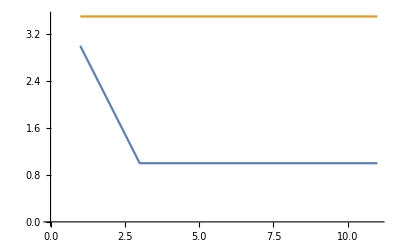

```mathematica
ListLinePlot[{definite2ArmBanditLearnList,Table[3.5,{x,definite2ArmBanditLearnList}] }] (* plot the learning curve of the automaton *)
```

Train a Tsetlin Automaton 10 times on an indefinite two-armed bandit problem.

```mathematica
indefinite2ArmBanditLearnList=NestList[ (* should learn 1, which usually (not always) wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{RandomVariate[NormalDistribution[0.75,.5]],RandomVariate[NormalDistribution[0.25,.5]]}]&,
4,10]
```

{4,3,2,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[indefinite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

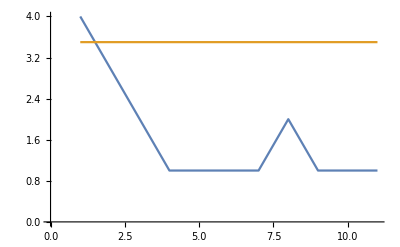

```mathematica
ListLinePlot[{indefinite2ArmBanditLearnList,Table[3.5,{x,indefinite2ArmBanditLearnList}] }](* plot the learning curve of the automaton *)
```

TsetlinWeightedReward rewards the Tsetlin Automaton if a random number from 0 to 1 is greater than the third argument, which is a number. In practical use, the third number is usually generated by applying a function.

```mathematica
TsetlinWeightedReward[t_Integer,si_Integer,pf_?NumericQ]:=
If[
RandomReal[]≤pf,
TsetlinReward[t,si],
t]
```

```mathematica
TsetlinWeightedReward[3,3,1]
```

3

```mathematica
TsetlinWeightedReward[3,3,1000]
```

2

TsetlinWeightedPunish is the punish equivalent of TsetlinWeightedReward.

```mathematica
TsetlinWeightedPunish[t_Integer,si_Integer,pf_?NumericQ]:=
If[
RandomReal[]≤pf,
TsetlinPunish[t,si],
t]
```

## Tsetlin Machine Basic Structure

Before the complete Tsetlin Machine head architecture is established, some heads important for building them need to be shown.

TsetlinClause[l, lneg] is a head that takes two arguments: the Tsetlin Automatons corresponding to the inputs as well as the ones corresponding to the negated inputs. TsetlinClauseNonNegated, when applied to a TsetlinClause, returns the list of automatons corresponding to the non-negated inputs. TsetlinClauseNegated returns the list of automatons corresponding to the negated inputs.

```mathematica
TsetlinClauseNonNegated[tc_TsetlinClause]:=tc[[1]]
```

```mathematica
TsetlinClauseNegated[tc_TsetlinClause]:=tc[[2]]
```

TsetlinOutput[l, f] is a head that takes two arguments: a list of conjunctive clauses and a function. It, when in use in a complete Tsetlin machine, applies the function to the list of clause outputs, and returns the final output. TsetlinOutputClauses outputs the list of TsetlinClauses of a TsetlinOutput, and TsetlinOutputFunction returns the function.

```mathematica
TsetlinOutputClauses[to_TsetlinOutput]:=to[[1]]
```

```mathematica
TsetlinOutputFunction[to_TsetlinOutput]:=to[[2]]
```

TsetlinMachine[lc, si] is a head that represents a single-layer Tsetlin Machine. It takes two arguments: a list of TsetlinOutputs and the state identifier it uses for all of it’s automatons. Here is an example of a Tsetlin Machine that takes three inputs and produces two outputs (where each output has two clauses):

```mathematica
tm0=TsetlinMachine[
{
TsetlinOutput[
{
TsetlinClause[
{3,4,3},{4,4,3}],
TsetlinClause[
{3,3,3},{4,4,4}]
},
Or],
TsetlinOutput[
{
TsetlinClause[
{6,5,2},{3,2,4}],
TsetlinClause[
{2,3,2},{1,2,5}]
},
Or]
},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]},3]

TsetlinMachineOutputs takes a TsetlinMachine as input, and outputs the list of outputs,

```mathematica
TsetlinMachineOutputs[tm_TsetlinMachine]:=tm[[1]]
```

```mathematica
TsetlinMachineOutputs[tm0]
```

{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]}

TsetlinMachineStateIdentifier takes a TsetlinMachine as input, and outputs the StateIdentifier of the machine.

```mathematica
TsetlinMachineStateIdentifier[tm_TsetlinMachine]:=tm[[2]]
```

```mathematica
TsetlinMachineStateIdentifier[tm0]
```

3

Inputs in a Tsetlin machine are given in binary. Numerical input can be given, but the numbers need to be converted to binary (a list of boolean values). As such, a maximum and minimum value need to be established. Hopefully I can develop a system so that the programmer does not need to worry about this (e.g. handled automatically) but for now this has to be done manually.
An example list of inputs to a Tsetlin machine: {False,False,False,False,True,True,False,True} (representing integer 13).

For the Tsetlin Automatons in the machine, 1 represents “exclude input” and 2 represents “include input”

TsetlinClauseSelectedInputs  takes a TsetlinClause, state identifier, and list of inputs. It returns a list of the inputs that the Tsetlin automaton of the clause have selected.

```mathematica
TsetlinClauseSelectedInputs[tc_TsetlinClause,si_Integer,li_List]:=
Last/@
Select[
Join[
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNonNegated[tc]),
li}],
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNegated[tc]),
Not/@li}]],
#[[1]]==2&]
```

```mathematica
TsetlinClauseSelectedInputs[ (* should output {True, True, False} *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

{True,True,False}

TsetlinClauseOutput takes a TsetlinClause, state identifier, and list of inputs as it’s arguments. It outputs either a 1 or 0, depending on the result of ANDing the selected inputs of the clause.

```mathematica
TsetlinClauseOutput[tc_TsetlinClause,si_Integer,li_List]:=
Fold[
And,
True,
TsetlinClauseSelectedInputs[tc,si,li]]
```

```mathematica
TsetlinClauseOutput[ (* should output False *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

False

TsetlinOutputResult takes a TsetlinOutput, state identifier, and list of inputs as it’s arguments. It returns the result of fold-applying the function of the TsetlinOutput to the TsetlinClause outputs calculated with the given state identifier and input.

```mathematica
TsetlinOutputResult[to_TsetlinOutput,si_Integer,li_List]:=
TsetlinOutputFunction[to][
Map[
TsetlinClauseOutput[#,si,li]&,
TsetlinOutputClauses[to]]]
```

```mathematica
TsetlinOutputResult[ (* should output True *)
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or@@#&],
3,
{True, False, True}]
```

True

TsetlinMachineCalculateOutputs takes a TsetlinMachine and a list of inputs as input, and outputs a list of the outputs. This is the way to apply trained Tsetlin machines.

```mathematica
TsetlinMachineCalculateOutputs[tm_TsetlinMachine,li_List]:=
Map[
TsetlinOutputResult[
#,
TsetlinMachineStateIdentifier[tm],
li]&,
TsetlinMachineOutputs[tm]]
```

```mathematica
TsetlinMachineCalculateOutputs[ (* Should return {True, False} *)
TsetlinMachine[
{
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or@@#&],
TsetlinOutput[
{TsetlinClause[
{1,5,1},
{2,1,1}],
TsetlinClause[
{1,1,2},
{5,1,2}]},
Or@@#&]},
3],
{True, False, True}]
```

{True,False}

## Initializing a Tsetlin Machine

First, some functions for building the structure of Tsetlin machines (introduced from bottom up).

TsetlinInitializeAutomatonList takes 2 arguments: the state identifier and the length of the input.

```mathematica
TsetlinInitializeAutomatonList[si_Integer,il_Integer]:=
Table[RandomInteger[]+si,il]
```

```mathematica
TsetlinInitializeAutomatonList[3,3]
```

{3,3,4}

TsetlinInitializeClause takes 2 arguments: the state identifier and the length of the input.

```mathematica
TsetlinInitializeClause[si_Integer,il_Integer]:=
Module[{
base=TsetlinInitializeAutomatonList[si,il]},
TsetlinClause[base,((2*si)-base)+1]]
```

```mathematica
TsetlinInitializeClause[3,3]
```

TsetlinClause[{3,4,3},{4,3,4}]

TsetlinInitializeOutput takes 4 arguments: the state identifier, the length of the input, the number of clauses per the output, and the output function.

```mathematica
TsetlinInitializeOutput[si_Integer,il_Integer,nc_Integer, f_]:=
TsetlinOutput[
Table[
TsetlinInitializeClause[si,il],
nc],
f]
```

```mathematica
TsetlinInitializeOutput[3,3,2,Or@@#&]
```

TsetlinOutput[{TsetlinClause[{3,3,4},{4,3,4}],TsetlinClause[{4,4,4},{4,3,3}]},Or]

TsetlinInitializeMachine takes 4 arguments: the state identifier, the length of the input, the number of clauses per each output, and a list consisting of the output functions (the length of the list implicitly is equal to the number of outputs).

```mathematica
TsetlinInitializeMachine[si_Integer,il_Integer,nc_Integer,lf_List]:=
TsetlinMachine[
Map[
TsetlinInitializeOutput[
si,
il,
nc,
#]&,
lf],
si]
```

```mathematica
TsetlinInitializeMachine[3,3,2,{Or@@#&}]
(* Should produce something like:
TsetlinMachine[
{TsetlinOutput[
{
TsetlinClause[
{3,4,3},
{4,4,3}],
TsetlinClause[
{4,3,4},
{4,3,3}]},
Or]},
3] *)
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{4,3,3},{3,3,4}]},Or]},3]

## Providing Feedback to a Tsetlin Machine

TsetlinAutomatonType1Feedback takes 5  arguments: an integer representing a Tsetlin automaton, the state identifier, the input that corresponds to the automaton,  the output of the clause that the automaton is a member of, and the s-value (precision). Output is an automaton that has been punished or rewarded accordingly.

```mathematica
TsetlinAutomatonType1Feedback[ta_Integer,si_Integer,i_?BooleanQ,co_?BooleanQ,s_?NumericQ]:=
If[
co (* clause output is 1 or 0? *),
If[
i, (* input is 1 or 0 *)
If[
(ta>si), (* input is included or excluded *)
TsetlinWeightedReward[ta,si,((s-1)/s)],
TsetlinWeightedPunish[ta,si,((s-1)/s)]],
If[
(ta>si), (* innput is included ot excluded *)
ta,
TsetlinWeightedReward[ta,si,(1/s)]]],
If[
(ta>si), (* input is included or excluded *)
TsetlinWeightedPunish[ta,si,(1/s)],
TsetlinWeightedReward[ta,si,(1/s)]]]
```

TsetlinAutomatonType2Feedback takes 5 arguments: an integer representing a Tsetlin automaton, the state identifier, the input that corresponds to the automaton, the output of the clause the automaton is a member of, and a boolean which is true if the TsetlinAutomaton corresponds to an original input, or false for a negated one.

```mathematica
TsetlinAutomatonType2Feedback[ta_Integer,si_Integer,i_?BooleanQ,co_?BooleanQ,it_?BooleanQ]:=
If[ 
(co==True),
If[
Not[i],
If[
Not[(TsetlinAction[ta,si]==2)],
If[
it,
TsetlinPunish[ta,si],
ta],
ta],
If[
Not[(TsetlinAction[ta,si]==2)],
If[
Not[it],
TsetlinPunish[ta,si],
ta],
ta],
ta],
ta]
```

TsetlinClauseType1Feedback takes 4 arguments: a TsetlinClause, the state identifier, the list of inputs, and an s-value. It outputs a TsetlinClause.

```mathematica
TsetlinClauseType1Feedback[tc_TsetlinClause,si_Integer,il_List,s_?NumericQ]:=
TsetlinClause[
MapThread[
TsetlinAutomatonType1Feedback[
#1,
si,
#2,
TsetlinClauseOutput[tc,si,il],
s]&,
{TsetlinClauseNonNegated[tc],
il}],
MapThread[
TsetlinAutomatonType1Feedback[
#1,
si,
#2,
TsetlinClauseOutput[tc,si,il],
s]&,
{TsetlinClauseNonNegated[tc],
Not/@il}]]
```

TsetlinClauseType2Feedback takes 3 arguments: a TsetlinClause, the state identifier, and the list of inputs. Output is a TsetlinClause.

```mathematica
TsetlinClauseType2Feedback[tc_TsetlinClause,si_Integer,il_List]:=
TsetlinClause[
MapThread[
TsetlinAutomatonType2Feedback[
#1,
si,
#2,
TsetlinClauseOutput[tc,si,il],
True]&,
{TsetlinClauseNonNegated[tc],
il}],
MapThread[
TsetlinAutomatonType2Feedback[
#1,
si,
#2,
TsetlinClauseOutput[tc,si,il],
False]&,
{TsetlinClauseNonNegated[tc],
Not/@il}]]
```

TsetlinOutputFeedback takes 6 arguments: a TsetlinOutput, the state identifier, a list of inputs, the desired output, an s-value, and a function. The function (called a feedbackDecider) should accept 6 inputs: the TsetlinOutput currently being trained, the index of the clause being currently processed, the state identifier, the list of inputs currently being trained on, the desired output, the s-value (precision). Output is a trained TsetlinOutput.

```mathematica
TsetlinOutputFeedback[to_TsetlinOutput,si_Integer,il_List,do_?BooleanQ,s_?NumericQ,fd_]:=
TsetlinOutput[
Map[
{(TsetlinOutputClauses[to][[#]]),
TsetlinClauseType1Feedback[
(TsetlinOutputClauses[to][[#]]),
si,
il,
s],
TsetlinClauseType2Feedback[
(TsetlinOutputClauses[to][[#]]),
si,
il]}[[(fd[to,#,si,il,do,s]+1)]]&,
Range[Length@TsetlinOutputClauses[to]]
],
TsetlinOutputFunction[to]]
```

```mathematica
TsetlinOutputFeedback[
(TsetlinMachineOutputs[
TsetlinInitializeMachine[
3,
3,
2,
{Or@@#&}]]⟦1⟧),
3,
{True,False,True},
True,
3.6,
2&]
```

TsetlinOutput[{TsetlinClause[{3,4,4},{3,4,4}],TsetlinClause[{4,4,3},{4,4,3}]},Or@@#1&]

TsetlinMachineFeedback takes x arguments: a TsetlinMachine, a list of inputs, the corresponding list of outputs, an s-value, and a feedbackDecider. Output is a TsetlinMachine that has been trained on the given set of inputs and outputs.

```mathematica
TsetlinMachineFeedback[tm_TsetlinMachine,il_List,ol_List,s_?NumericQ,fd_]:=
TsetlinMachine[
MapThread[
TsetlinOutputFeedback[
#1,
TsetlinMachineStateIdentifier[tm],
il,
#2,
s,
fd]&,
{TsetlinMachineOutputs[tm],
ol}],
TsetlinMachineStateIdentifier[tm]]
```

```mathematica
TsetlinMachineFeedback[
TsetlinInitializeMachine[
3,
3,
2,
{Or@@#&}],
{True,False,True},
{True},
3.5,
#2&]
```

```mathematica
TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{2,4,3}],TsetlinClause[{3,4,3},{3,4,3}]},Or@@#1&]},3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{2,4,3}],TsetlinClause[{3,4,3},{3,4,3}]},Or@@#1&]},3]

## Testing and Training a Tsetlin Machine

First of all, some functions used during training by the Tsetlin machine need to be defined.

TsetlinAdvancedBaseFunction takes a list of the outputs of TsetlinClauses as input and outputs the sum of the clauses at odd indexes - the sum of the clauses at even indexes.

```mathematica
TsetlinAdvancedBaseFunction[lc_List]:=
Total[lc[[;;;;2]]]-Total[lc[[2;;;;2]]]
```

```mathematica
TsetlinAdvancedBaseFunction[{1,2,3,4,5,6,7,8}]
```

-4

TsetlinAdvancedOutputFunction takes a list of the output of clauses, and returns a True or False depending on if the output of TsetlinAdvancedBaseFunction is greater or less than 0.

```mathematica
TsetlinAdvancedOutputFunction[lc_List]:=
(TsetlinAdvancedBaseFunction[lc/.{True->1,False->0}]≥0)
```

TsetlinAdvancedFeedbackDecider takes 7 inputs: the TsetlinOutput currently being trained, the index of the clause being currently processed, the state identifier, the list of inputs currently being trained on, the desired output, the s-value (precision), and a T-value (threshold).

```mathematica
TsetlinAdvancedFeedbackDecider[to_TsetlinOutput,ci_Integer,si_Integer,il_List,do_?BooleanQ,s_?NumericQ,t_Integer]:=
If[
do==True,
If[
RandomReal[]≤
((t-Max[
-t,
Min[
t,
TsetlinAdvancedBaseFunction[
((TsetlinClauseOutput[
#,
si,
il
]&/@
TsetlinOutputClauses[to])/.{True->1,False->0})]]])/
2t),
2-Mod[ci,2],
0],
If[
RandomReal[]≤
((t+Max[
-t,
Min[
t,
TsetlinAdvancedBaseFunction[
((TsetlinClauseOutput[
#,
si,
il
]&/@
TsetlinOutputClauses[to])/.{True->1,False->0})]]])/
2t),
2-Mod[ci+1,2],
0]]
```

```mathematica
TsetlinAdvancedFeedbackDecider[
TsetlinMachineOutputs[
TsetlinInitializeMachine[
3,
2,
3,
{TsetlinAdvancedOutputFunction}]][[1]],
1,
3,
{True,False},
False,
3,
0]
```

0

It is important to establish methods of how to test a Tsetlin Machine, to use when training later.

TsetlinMachineTest takes 3 arguments: a TsetlinMachine, a list of input lists, and a list of corresponding expected output lists. It returns a numeric percentage of correct answers by the TsetlinMachine. It has the following options that can be set to true or false: EchoTestResults (whether to echo test results or not, False by default), ReturnTestResults (whether to return test results (true) or tm argument (false). On by default), SowTestResults (Whether or not to sow test results. Off by default.

```mathematica
TsetlinMachineTest[tm_TsetlinMachine,ill_List,oll_List,OptionsPattern[{EchoTestResults-> False,ReturnTestResults-> True,SowTestResults-> False}]]:=
Module[{f=
N[(Total@
(MapThread[
(TsetlinMachineCalculateOutputs[
tm,
#1]==#2)&,
{ill,oll}]/.{False->0,True->1}))/
(Length@ill)]},
(If[
OptionValue[EchoTestResults]==True,
Echo[f,"Percent correct:"]];
If[
OptionValue[SowTestResults] == True,
Sow[f]];
If[
OptionValue[ReturnTestResults] == True,
Return[f],
Return[tm]])]
```

```mathematica
TsetlinMachineTest[
TsetlinInitializeMachine[
3,
2,
2,
{Or@@#&}],
{{True,True},
{True,False}},
{{False},{True}},EchoTestResults->True]
```

0.5

0.5

TsetlinMachineUpdate takes x arguments: a TsetlinMachine, a list of list of inputs, a list of list of outputs, an s-value, and a feedbackDecider.

TsetlinMachineTrain takes 8 inputs: a TsetlinMachine, a list of list of training inputs, a list of list of training outputs, a list of list of testing inputs, a list of list of testing outputs, an s-value, a feedbackDecider, and a stop criteria. Output is a trained TsetlinMachine. A stop criteria  can be one of the following: a real number less than or equal to 1 (representing goal accuracy), an integer 1 or greater (representing number of times to train), a real number 1 or greater (representing seconds to train). It has the same options as TsetlinMachineTest

```mathematica
TsetlinMachineTrain[tm_TsetlinMachine,ill_List,oll_List,till_List,toll_List,s_?NumericQ,fd_,sc_?NumericQ,OptionsPattern[{EchoTestResults-> False,ReturnTestResults-> False,SowTestResults-> False}]]:=
(looper=
Which[
IntegerQ[sc],0,
sc>1,AbsoluteTime[]];
NestWhile[
({trainInput,trainOutput}=RandomChoice@Transpose@{ill,oll};
TsetlinMachineFeedback[
TsetlinMachineTest[#1,till,toll,ReturnTestResults->False,EchoTestResults->OptionValue[EchoTestResults],SowTestResults->OptionValue[SowTestResults]],
trainInput,
trainOutput,
s,
fd])&,
tm,
Which[
IntegerQ[sc],looper++<sc,
sc>1,AbsoluteTime[]-looper<sc,
sc≤1,TsetlinMachineTest[#,till,toll]<sc]&])
```

## Actually Training a Tsetlin Machine

```mathematica
TsetlinMachineTrain[
TsetlinInitializeMachine[
100,
2,
20,
{TsetlinAdvancedOutputFunction}],
{{False,False},{False,True},{True,False},{True,True}},
{{False},{True},{True},{False}},
{{False,False},{False,True},{True,False},{True,True}},
{{False},{True},{True},{False}},
3.6,
TsetlinAdvancedFeedbackDecider[#1,#2,#3,#4,#5,#6,15]&,
30,
EchoTestResults->True]
```

Percent correct: 0.75

Percent correct: 0.5

Percent correct: 0.5

Percent correct: 0.5

«9 more identical outputs»

Percent correct: 0.25

Percent correct: 0.25

Percent correct: 0.75

Percent correct: 0.5

Percent correct: 0.5

Percent correct: 0.5

«11 more identical outputs»

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{95,101},{95,101}],TsetlinClause[{100,100},{100,101}],TsetlinClause[{94,101},{94,101}],TsetlinClause[{100,100},{101,101}],TsetlinClause[{100,102},{100,102}],TsetlinClause[{101,99},{101,100}],TsetlinClause[{95,100},{95,100}],TsetlinClause[{101,99},{101,98}],TsetlinClause[{99,101},{99,101}],TsetlinClause[{101,98},{102,99}],TsetlinClause[{98,101},{98,101}],TsetlinClause[{99,100},{99,101}],TsetlinClause[{99,101},{99,101}],TsetlinClause[{100,101},{100,101}],TsetlinClause[{101,97},{101,97}],TsetlinClause[{97,102},{97,102}],TsetlinClause[{100,100},{100,100}],TsetlinClause[{100,101},{100,101}],TsetlinClause[{101,94},{101,94}],TsetlinClause[{99,101},{100,101}]},TsetlinAdvancedOutputFunction]},100]